```mathematica
SetDirectory[NotebookDirectory[]];
<<MaTeX`
```

```mathematica
Get["../../lib/lib2.m"];
Get["../../lib/util.m"];
```

```mathematica
SetOptions[MaTeX,"Preamble"->{"\\usepackage{physics,mathtools,newtxtext,newtxmath}"}, FontSize->12];
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"]
texStyle={FontFamily->"Times",FontSize->12};
```

```mathematica
cm = 72/2.54;
```

```mathematica
plotsDir = "../../../plots/plots-thesis";
If[!DirectoryQ[plotsDir], CreateDirectory[plotsDir]];
```

```mathematica
data = Import["../../../runs/Trials/N9K9/66436371.dat"];
```

```mathematica
changeNK[9, 9];
```

```mathematica
l1 = (1+(k-1)(($N)^2-1)+a)/.{k->1, a->1};
l2 = (1+(k-1)(($N)^2-1)+a)/.{k->1, a->5};
l3 = (1+(k-1)(($N)^2-1)+a)/.{k->7, a->3};
```

```mathematica
fig = ListPlot[{data[[All, {1,l1}]], data[[All, {1,l2}]], data[[All, {1,l3}]]},
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
FrameLabel->MaTeX/@{"t", "x^i_a(t)"},
FrameTicks->{{With[{ticks=-0.3+0.1Range[0,6]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=20Range[0,8]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
PlotLegends->Placed[MaTeX/@{"x^1_1(t)", "x^1_5(t)", "x^7_3(t)"}, {Bottom, Center}],
PlotRange->{{0, 80}, Full},
ImageSize->14cm,
Joined->True
];
```

```mathematica
Magnify[fig, 1]
```

-Graphics-

```mathematica
Export[plotsDir<>"/1-elements.pdf", fig]
```

../../../plots/plots-thesis/1-elements.pdf

```mathematica
rad = radius/@data;
```

```mathematica
fig2 = ListPlot[rad,
Frame->True,
FrameStyle->Black,
BaseStyle->texStyle,
PlotTheme->"Scientific",
GridLines->None,
FrameLabel->MaTeX/@{"t", "\\Tr X^i X^i"},
FrameTicks->{{With[{ticks=0+Range[0,6]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None},{With[{ticks=20Range[0,8]//Chop},Thread[{ticks,MaTeX[ticks,"DisplayStyle"->False]}]],None}},
PlotRange->{{0, 80}, Full},
ImageSize->14cm,
Joined->True,
PlotRangePadding->{1.0, 0.1}
];
```

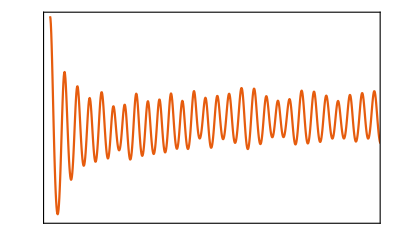

```mathematica
Magnify[fig2, 1]
```

```mathematica
Export[plotsDir<>"/1-trX2.pdf", fig2]
```

../../../plots/plots-thesis/1-trX2.pdf